# Soundex

Computes the Soundex phonetic identifier of a word.

## DefinitionDefinitionDefine your function using the name you gave in the Title line above. You can add input cells and extra code to define additional input cases or prerequisites. All definitions, including dependencies, will be included in the generated resource function. This section should be evaluated before creating the Examples section below.

```mathematica
Clear[Soundex];
Soundex[word_String]:=
Block[{sword=ToLowerCase[word],f,res},
(*1*)
f=StringTake[sword,{1,1}];
res=StringDelete[StringTake[sword,{2,-1}],RegularExpression["[hw]"]];

(*2*)res=StringReplace[f<>res,{RegularExpression["[bfpv]"]->"1",RegularExpression["[cgjkqsxz]"]->"2",RegularExpression["[dt]"]->"3","l"->"4",RegularExpression["[mn]"]->"5","r"->"6"}];

(*3*)
res=StringReplace[res,(x_~~x_):>x];

(*4*)
res=StringDelete[res,RegularExpression["[aeiouy]"]];

(*5*)
If[StringLength[res]==0,res=f];
res=StringReplace[res,StartOfString~~DigitCharacter:>f];

(*6*)
If[StringLength[res]<4,res=res<>"000";];
res=StringTake[res,4];

res
];
```

## Documentation

### UsageUsageDocument input usage cases by first typing an input structure, then pressing to add a brief explanation of the function’s behavior for that structure. Pressing repeatedly will create new cases as needed. Every input usage case defined above should be demonstrated explicitly here. See existing documentation pages for examples.

Soundex[word]

finds a Soundex phonetic identifier of the string word .

### Details & OptionsDetails & OptionsGive a detailed explanation of how the function is used and configured (e.g. acceptable input types, result formats, options specifications, background information). This section may include multiple cells, bullet lists, tables, hyperlinks and additional styles/structures as needed. Add any other information that may be relevant, such as when the function was first discovered or how and why it is used within a given field. Include all relevant background or contextual information related to the function, its development, and its usage.

The goal of the Soundex algorithm is homophones to be encoded with the same identifiers. (Therefore same sounding words would match regardless of spelling variants or misspellings.)

## ExamplesExamplesDemonstrate the function’s usage, starting with the most basic use case and describing each example in a preceding text cell. Within a group, individual examples can be delimited by inserting page breaks between them (either using "[Right-click]"" ▶ ""Insert Page Break" between cells or through the menu using "Insert"" ▶ ""Page Break"). Examples should be grouped into Subsection and Subsubsection cells similarly to existing documentation pages. Here are some typical Subsection names and the types of examples they normally contain: "◼ ""Basic Examples: "most basic function usage "◼ ""Scope: "input and display conventions, standard computational attributes (e.g. threading over lists) "◼ ""Options: "available options and parameters for the function "◼ ""Applications: "standard industry or academic applications "◼ ""Properties and Relations: "how the function relates to other functions "◼ ""Possible Issues: "limitations or unexpected behavior a user might experience "◼ ""Neat Examples: "particularly interesting, unconventional, or otherwise unique usage

### Basic Examples

Find the Soundex identifier of a word:

```mathematica
Soundex["horror"]
```

h660

Soundex identifier of a misspelled word (the result is the same as above):

```mathematica
Soundex["horur"]
```

h660

### Scope

The character case does not matter:

```mathematica
Soundex["dancer"]
```

d526

```mathematica
Soundex["DANCER"]
```

d526

Digits are not processed and become part of the result:

```mathematica
Soundex["d4ncer"]
```

d452

### Applications

Compute an association of dictionary words and corresponding Soundex codes:

```mathematica
AbsoluteTiming[
codes=Association@Map[#->Soundex[#]&,DictionaryLookup["*"]];
]
```

{2.27908,Null}

Show the top 20 most “popular” Soundex codes:

```mathematica
top=TakeLargestBy[Tally[Values[codes]],#⟦2⟧&,20]
```

{{t652,403},{c536,317},{p632,235},{c623,219},{c526,214},{p625,212},{c516,212},{s162,208},{p623,203},{p612,198},{s362,193},{c535,190},{a200,183},{s163,182},{p622,182},{c512,176},{s352,170},{s363,165},{p626,163},{s520,163}}

Show that the Soundex codes adhere to the Pareto principle:

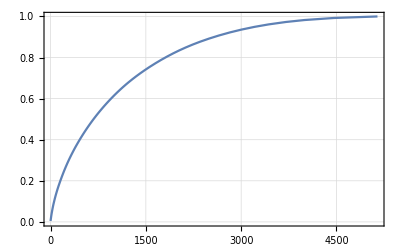

```mathematica
freqs=SortBy[Tally[Values[codes]],-#⟦2⟧&]⟦All,2⟧;
freqs=Accumulate[freqs]/Total[freqs];
ListLinePlot[freqs,PlotTheme->"Detailed"]
```

Show the words corresponding to one of the top Soundex codes:

```mathematica
GroupBy[Normal[codes],#⟦2⟧&,#⟦All,1⟧&][top⟦20,1⟧]
```

{sames,samosa,Sancho,sanes,sang,Sang,sangs,sank,Sanka,sans,saunas,sawing,saying,sayings,scams,scans,scenes,scenic,schemas,schemes,schmoes,schmooze,schmuck,schnook,schnooks,schnoz,science,scions,sconce,scones,scums,seams,seance,seeing,seeings,seems,seines,semis,Seneca,sens,sense,sewing,shames,shams,shanghai,Shanghai,shank,shanks,Shawnees,shewing,shimmies,shims,shines,shinnies,shins,shoeing,shooing,showiness,showing,showings,shuns,shying,shyness,Siamese,Sihanouk,Sims,since,sines,sinews,sing,singe,sings,sink,sinks,sins,sinuous,sinus,skeins,skewing,skewness,skiing,skims,skins,skunk,skunks,skying,smack,smash,smock,smog,smoggy,smogs,smoke,smokey,Smokey,smoky,smooch,smoochy,smug,smugs,snack,snag,snags,snake,Snake,snaky,snazzy,sneak,sneaks,sneaky,sneeze,snick,snog,snogs,snooze,snows,snowshoe,snug,snugs,someways,Somoza,song,Songhai,Songhua,songs,sonic,sonics,Sonja,sonnies,sons,soonish,sowing,Soyinka,squamous,squeamish,suing,sumac,sums,sung,Sung,sunk,sunks,sunnies,Sunnis,suns,swains,swamis,swank,swanks,swanky,swans,Swansea,swaying,swims,swines,swing,swings,swinish,swoons,swung,sync,syncs,Synge}

### Properties and Relations

### Possible Issues

### Neat Examples

Pick some words:

```mathematica
SeedRandom[332];
words=RandomWord["CommonWords",12]
```

{reversal,reheat,charlatanism,fistulous,conformism,headdress,maidenhair,subculture,conservatism,laddie,crossbeam,negotiator}

Introduce random misspellings:

```mathematica
misspelled=MapThread[RandomChoice[{StringDrop[#1,{#2}],StringReplacePart[#,RandomChoice[CharacterRange["a","x"]],{#2,#2}]}]&,{words,RandomInteger[{1,StringLength[#]}]&/@words}]
```

{reveral,rehead,charlatasism,fistuous,conformsm,hsaddress,maienhair,subcultpre,consedvatism,ladie,vrossbeam,negotiatow}

Compare the corresponding Soundex codes for both word sets:

```mathematica
Tally[MapThread[Soundex[#1]==Soundex[#2]&,{words,misspelled}]]
```

{{False,6},{True,6}}

See do the Soundex codes of words are found in the Soundex codes of the spelling correction lists:

```mathematica
MapThread[MemberQ[Soundex/@SpellingCorrectionList[#2],Soundex[#1]]&,{words,misspelled}]
```

{True,True,True,True,True,True,True,True,True,True,True,True}

## Source & Additional Information

### Contributed ByContributed ByEnter the name of the person, people or organization that should be publicly credited with contributing this function.

Anton Antonov

### KeywordsKeywordsList relevant terms (e.g. functional areas, algorithm names, related concepts) that should be used to include the function in search results.

Soundex

homophones

encoding

phonetic algorithm

### Categories

Cloud & Deployment |  Core Language & Structure
 Data Manipulation & Analysis |  Engineering Data & Computation
 External Interfaces & Connections |  Financial Data & Computation
 Geographic Data & Computation |  Geometry
 Graphs & Networks |  Higher Mathematical Computation
 Images |  Just For Fun
 Knowledge Representation & Natural Language |  Machine Learning
 Notebook Documents & Presentation |  Programming Utilities
 Repository Tools |  Scientific and Medical Data & Computation
 Social, Cultural & Linguistic Data |  Sound
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Time-Related Computation
 User Interface Construction |  Visualization & Graphics

### Related SymbolsRelated SymbolsList up to twenty documented, system-level Wolfram Language symbols related to the function.

Encode

### Related Resource ObjectsRelated Resource ObjectsList the names of published resource objects from any Wolfram repository that are related to this function.

### Source/Reference CitationSource/Reference CitationGive a bibliographic-style citation for the original source of the function and/or its components (e.g. a published paper, algorithm, or code repository).

Wikipedia entry “Soundex”, https://en.wikipedia.org/wiki/Soundex .

### LinksLinksList additional URLs or hyperlinks for external information related to the function.

https://github.com/antononcube/MathematicaForPrediction/blob/master/Misc/Soundex.m

### TestsTestsSpecify an optional list of tests for verifying that the function is working properly in any environment. Tests can be specified as Input/Output cell pairs or as symbolic VerificationTest expressions for including additional options.

```mathematica
SeedRandom[1231]
words=Select[RandomWord["CommonWords",1200],StringLength[#]>4&];
misspelled=MapThread[RandomChoice[{StringDrop[#1,{#2}],StringReplacePart[#,RandomChoice[CharacterRange["a","x"]],{#2,#2}]}]&,{words,RandomInteger[{2,StringLength[#]-1}]&/@words}];
```

```mathematica
Map[Soundex,words]==Map[Soundex,ToUpperCase[words]]
```

True

```mathematica
HammingDistance[Map[Soundex,words],Map[Soundex,misspelled]]/Length[words]<0.5
```

True

## Author Notes

Soundex is a 100 years old algorithm, so there are better, upgraded algorithms based on its core idea.

## Submission NotesSubmission NotesEnter any additional information that you would like to communicate to the reviewer here. This section will not be included in the published resource.

Additional information for the reviewer.